numeric simulation

```mathematica
Quit[]
```

```mathematica
dispSimp = {a_[t]->a,Cos[a_]->c[a],Sin[a_]->s[a],Subscript[ⅈ, i_,zz]->Subscript[I, i]};
```

original equations:

```mathematica
(quadEqNominal=EulerEquations[L,{(*Subscript[x, 1][t],Subscript[y, 1][t],Subscript[θ, 1][t],Subscript[x, 2][t],Subscript[y, 2][t],Subscript[θ, 2][t],*)Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},t](*[[All,1]]*)(*==Q*)//Simplify)//MatrixForm//TraditionalForm
```

((k_1 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p x_p''(t)
(k_1 (-1/2 h_p cos(θ_p(t))+1/2 l_p sin(θ_p(t))-y_p(t)+y_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (-1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))-y_p(t)+y_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p (g+y_p''(t))
ⅈ_(p,zz) θ_p''(t)+(k_1 (h_p (x_1(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_1(t)-y_p(t)) sin(θ_p(t)))+l_p (x_1(t) (-sin(θ_p(t)))+x_p(t) sin(θ_p(t))+(y_1(t)-y_p(t)) cos(θ_p(t)))) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (h_p (x_2(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_2(t)-y_p(t)) sin(θ_p(t)))+l_p (x_2(t) sin(θ_p(t))-x_p(t) sin(θ_p(t))+(y_p(t)-y_2(t)) cos(θ_p(t)))) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(2 √((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==0)

```mathematica
non-conserving forces:
aerodynamic =  f(OverDot[Subscript[x, p]],OverDot[Subscript[y, p]],Subscript[θ, p], Subscript[w, x],Subscript[w, y]) , w for wind components. = f(Subscript[relV, x],Subscript[relV, y]) , relV is relative to air 
dumping (structural)= f(OverDot[Subscript[l, i]])=f(OverDot[Subscript[x, i]],OverDot[Subscript[y, i]],OverDot[Subscript[x, p]],OverDot[Subscript[y, p]])
```

non dim the full equations

```mathematica
(smallEqs=quadEqNominal/.terms2/.terms3)//MatrixForm
```

((r1x k_1 (a-L0_1))/(√(a^2))+(r2x k_2 (b-L0_2))/(√(b^2))==m_p x_p''[t]
(r1y k_1 (a-L0_1))/(√(a^2))+(r2y k_2 (b-L0_2))/(√(b^2))==m_p (g+y_p''[t])
(c1 k_1 (a-L0_1))/(√(a^2))+(c2 k_2 (b-L0_2))/(√(b^2))+ⅈ_(p,zz) θ_p''[t]==0)

NonDimEq manually settings the terms:

```mathematica
OverTilde[Subscript[y, p]][t]=Subscript[y, p][t] /Subscript[L0, 1]  or any other of the lengths varialbes (Subscript[x, p],r1x,r1y,r2x,r2y,Subscript[h, p],Subscript[l, p])
t=τ/Subscript[ω, s]
Subscript[ω, s]^2=(Subscript[k, 1]/Subscript[m, p])[g/l=1/s^2]
A is non-dimentional  form of 'a'
B is non-dimentional  form of 'b'
```

(((1-1/A) k_1 L0_1 r1x)/m_p+(k_2 L0_1 r2x (1-L0_2/(B L0_1)))/m_p==L0_1 ω_s^2 x_p''(t)
((1-1/A) k_1 L0_1 r1y)/m_p+(k_2 L0_1 r2y (1-L0_2/(B L0_1)))/m_p-g==L0_1 ω_s^2 y_p''(t)
-((1-1/A) c_1 k_1 L0_1^2)/(ⅈ_(p,zz))-(c_2 k_2 L0_1^2 (1-L0_2/(B L0_1)))/(ⅈ_(p,zz))==ω_s^2 θ_p''(t))

```mathematica
(*Subscript[Delta, Equilibrium]=(Subscript[m, p] g)/Subscript[k, i]*)
```

```mathematica
greekTerms={
Subscript[k, 2]/Subscript[k, 1]->κ,
Subscript[L0, 2]/Subscript[L0, 1]->ℒ,
Subscript[k, 1]/Subscript[m, p]->Subscript[ω, s]^2,
(Subscript[m, p] Subscript[L0, 1]^2)/Subscript[I, p](=(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p] Subscript[ω, s]^2))->α,
g/(Subscript[L0, 1] Subscript[ω, s]^2)(=(g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))->γ
}
```

```mathematica
(NonDimEq={
Subscript[ω, s]^2 Subscript[L0, 1](1-1/A)r1x +κ Subscript[ω, s]^2  Subscript[L0, 1](1-1/B ℒ)r2x ==Subscript[L0, 1] Subscript[ω, s]^2 Subscript[x, p]''[t],
Subscript[ω, s]^2 Subscript[L0, 1](1-1/A)r1y +κ Subscript[ω, s]^2  Subscript[L0, 1](1-1/B ℒ)r2y -g/(Subscript[L0, 1] Subscript[ω, s]^2)Subscript[L0, 1] Subscript[ω, s]^2==Subscript[L0, 1] Subscript[ω, s]^2 Subscript[y, p]''[t],
Subscript[k, 1]/(-Subscript[ⅈ, p,zz]) Subscript[L0, 1]^2/Subscript[ω, s]^2 Subscript[ω, s]^2(1-1/A)Subscript[c, 1] +κ Subscript[k, 1]/(-Subscript[ⅈ, p,zz]) Subscript[L0, 1]^2/Subscript[ω, s]^2 Subscript[ω, s]^2(1-1/B ℒ)Subscript[c, 2]==Subscript[ω, s]^2 Subscript[θ, p]''[t]
})//Flatten//MatrixForm//TraditionalForm
```

((1-1/A) L0_1 r1x ω_s^2+κ L0_1 r2x (1-ℒ/B) ω_s^2==L0_1 ω_s^2 x_p''(t)
(1-1/A) L0_1 r1y ω_s^2+κ L0_1 r2y (1-ℒ/B) ω_s^2-g==L0_1 ω_s^2 y_p''(t)
-((1-1/A) c_1 k_1 L0_1^2)/(ⅈ_(p,zz))-(c_2 κ k_1 L0_1^2 (1-ℒ/B))/(ⅈ_(p,zz))==ω_s^2 θ_p''(t))

```mathematica
𝒳^(..)=({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/A)Subscript[𝒱, 1]+κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/B ℒ)Subscript[𝒱, 2]-({{0}, {γ}, {0}})-Cmat.𝒳̇+Forces
```

```mathematica
𝒳^(..)=f[𝒳,𝒳̇]
```

```mathematica
Quit[]
```

```mathematica
𝒳=({{Subscript[x, p][t]}, {Subscript[y, p][t]}, {Subscript[θ, p][t]}})(*//Flatten*)
greekTermsSymetricCase={
(*Subscript[k, 2]/Subscript[k, 1]->*)κ->1,
(*Subscript[L0, 2]/Subscript[L0, 1]->*)ℒ->1
}
greekTermsGeneral={
(*Subscript[k, 2]/Subscript[k, 1]->*)κ->1,
(*Subscript[L0, 2]/Subscript[L0, 1]->*)ℒ->1,
(*Subscript[k, 1]/Subscript[m, p]->*)Subscript[ω, s]^2->1,
(*(Subscript[m, p] Subscript[L0, 1]^2)/Subscript[I, p](=(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p] Subscript[ω, s]^2))->*)α->1,
(*g/(Subscript[L0, 1] Subscript[ω, s]^2)(=(g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))-> *)γ->1 (* make sure it is not over-determined constant *)

}
(* already here : replacing all former Subscript[h, p],Subscript[l, p] with new 2 Subscript[h, p],2 Subscript[l, p]*)
A(*->√(r1x^2+r1y^2)*)=√((Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 1][t]-Subscript[x, p][t]))^2+(- Cos[Subscript[θ, p][t]] Subscript[h, p]+ Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 1][t]-Subscript[y, p][t]))^2)

B(*->√(r2x^2+r2y^2)*)=√((Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 2][t]-Subscript[x, p][t]))^2+(- Cos[Subscript[θ, p][t]] Subscript[h, p]- Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 2][t]-Subscript[y, p][t]))^2)
(*Subscript[c, 1](*->dr1+dr2*)=Subscript[l, p] (-Sin[Subscript[θ, p][t]] (Subscript[x, 1][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 1][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))
Subscript[c, 2](*->dr3+dr4*)=Subscript[l, p] (Sin[Subscript[θ, p][t]] (Subscript[x, 2][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 2][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))*)
Subscript[𝒱, 1](*=({{r1x}, {r1y}, {Subscript[c, 1]}})*)=({{(Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 1][t]-Subscript[x, p][t]))}, {(- Cos[Subscript[θ, p][t]] Subscript[h, p]+ Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 1][t]-Subscript[y, p][t]))}, {Subscript[l, p] (-Sin[Subscript[θ, p][t]] (Subscript[x, 1][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 1][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))}})
Subscript[𝒱, 2](*=({{r2x}, {r2y}, {Subscript[c, 2]}})*)=({{(Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 2][t]-Subscript[x, p][t]))}, {(- Cos[Subscript[θ, p][t]] Subscript[h, p]- Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 2][t]-Subscript[y, p][t]))}, {Subscript[l, p] (Sin[Subscript[θ, p][t]] (Subscript[x, 2][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 2][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))}})
Cmat=({{Subscript[c, 1], 0, 0}, {0, Subscript[c, 2], 0}, {0, 0, Subscript[c, 3]}});
nameChange={Subscript[l, p]->Subscript[w, p]};
"equations with no general forces :"
EOM=D[𝒳,{t,2}]==(({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/A)).Subscript[𝒱, 1]+(κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/B ℒ)).Subscript[𝒱, 2]-({{0}, {γ}, {0}})-Cmat.D[𝒳,{t,1}]  //.nameChange//Flatten;
```

{{x_p[t]},{y_p[t]},{θ_p[t]}}

{κ→1,ℒ→1}

{κ→1,ℒ→1,ω_s^2→1,α→1,γ→1}

√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+x_1[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p+y_1[t]-y_p[t])^2)

√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p-Sin[θ_p[t]] l_p+y_2[t]-y_p[t])^2)

{{Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+x_1[t]-x_p[t]},{-Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p+y_1[t]-y_p[t]},{l_p (-Sin[θ_p[t]] (x_1[t]-x_p[t])+Cos[θ_p[t]] (y_1[t]-y_p[t]))+h_p (Cos[θ_p[t]] (x_1[t]-x_p[t])+Sin[θ_p[t]] (y_1[t]-y_p[t]))}}

{{Sin[θ_p[t]] h_p-Cos[θ_p[t]] l_p+x_2[t]-x_p[t]},{-Cos[θ_p[t]] h_p-Sin[θ_p[t]] l_p+y_2[t]-y_p[t]},{h_p (Cos[θ_p[t]] (x_2[t]-x_p[t])+Sin[θ_p[t]] (y_2[t]-y_p[t]))+l_p (Sin[θ_p[t]] (x_2[t]-x_p[t])+Cos[θ_p[t]] (-y_2[t]+y_p[t]))}}

equations with no general forces :

```mathematica
a
```

-Graphics-

```mathematica
Clear[a]
```

```mathematica
dispNoTime={a_[t]->a};(*
EOM/.dispNoTime/.greekTermsSymetricCase//Flatten(*//MatrixForm*)(*//TraditionalForm*);
EOM/.dispNoTime/.greekTermsSymetricCase//Flatten(*//MatrixForm*)//TraditionalForm*)
```

```mathematica
(*numerics={Subscript[h, p]->0.1,Subscript[w, p]->1,Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->0,α->0.04,γ->2}*)
(*EOM//.greekTermsSymetricCase//.numerics//Flatten//TraditionalForm*)
```

{h_p→0.1,w_p→1,x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0,α→0.04,γ→2}

(x_p''(t)
y_p''(t)
θ_p''(t))==((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2) (1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2)))+(cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)) (1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2)))
(1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2))) (-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))+(1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2))) (-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))-2
-0.04 (1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2))) (sin(θ_p(t)) (2-x_p(t))+cos(θ_p(t)) y_p(t)+0.1 (cos(θ_p(t)) (2-x_p(t))-sin(θ_p(t)) y_p(t)))-0.04 (1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2))) (sin(θ_p(t)) x_p(t)-cos(θ_p(t)) y_p(t)+0.1 (-cos(θ_p(t)) x_p(t)-sin(θ_p(t)) y_p(t))))

```mathematica
(*EquibInputConditions={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]}*)
```

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→y_1[t]}

```mathematica
(*(SymetricEquib=EOM/.nameChange/.greekTermsSymetricCase(*/.equibTerms*)//.EquibInputConditions)//MatrixForm//TraditionalForm*)
```

(x_p''(t)
y_p''(t)
θ_p''(t))==((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2)))+(sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2)))-c_1 x_p'(t)
-γ+(1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))+(1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))-c_2 y_p'(t)
-α (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) (2 w_p-x_p(t))+cos(θ_p(t)) y_p(t))+h_p (cos(θ_p(t)) (2 w_p-x_p(t))-sin(θ_p(t)) y_p(t)))-α (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) x_p(t)-cos(θ_p(t)) y_p(t))+h_p (-cos(θ_p(t)) x_p(t)-sin(θ_p(t)) y_p(t)))-c_3 θ_p'(t))

```mathematica
NumericParametersTest={Subscript[k, 1]->200, Subscript[k, 2]->Subscript[k, 1]+0,Subscript[L0, 1]->2,Subscript[L0, 2]->Subscript[L0, 1]+0,Subscript[m, p]->2,Subscript[h, p]->0.1,Subscript[w, p]->1,g->9.81}
NumericEquibInputs={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->0(*,α->0.04,γ->2*)}
NumericStructuralDamping={Subscript[c, 1]->1,Subscript[c, 2]->1,Subscript[c, 3]->1};
NumericNonStructuralDamping={Subscript[c, 1]->0,Subscript[c, 2]->0,Subscript[c, 3]->0};
greekTermsGeneralForTest={
κ->Subscript[k, 2]/Subscript[k, 1],
ℒ->Subscript[L0, 2]/Subscript[L0, 1],
Subscript[ω, s]^2->Subscript[k, 1]/Subscript[m, p],
α->(3 Subscript[L0, 1]^2)/(Subscript[w, p]^2+Subscript[h, p]^2),
γ->((g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))
}
(*g/Subscript[L0, 1]/.NumericParametersTest*)
NumericTestParams=greekTermsGeneralForTest//.NumericParametersTest
```

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0}

{κ→k_2/k_1,ℒ→L0_2/L0_1,ω_s^2→k_1/m_p,α→(3 L0_1^2)/(h_p^2+w_p^2),γ→(g m_p)/(k_1 L0_1)}

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

“(*simple case testings:*)”

```mathematica
(*trajectory:
τ=0: y^(..)=1m/s^2  until Subscript[y, 1]=Subscript[y, 2]=10 Subscript[L0, 1]
    y^(..)=-1m/s^2 until OverDot[Subscript[y, 1]]=OverDot[Subscript[y, 2]]=0
Subscript[x, 1]^(..)=Subscript[x, 2]^(..)=1m/s^2  until OverDot[Subscript[x, 1]]=OverDot[Subscript[x, 2]]=2m/s
disterbunce can be input by Subscript[x, 1]+=5 Subscript[L0, 1] over 1/(100 √Subscript[ω, s])*)
```

```mathematica
(* greekTermsSymetricCase must be used again because this is where the equilibrium point is refering to .
EquibInputConditions might be turned of later for better investigation *)
(SymetricEOMtoInvestigate=EOM/.greekTermsSymetricCase//.EquibInputConditions)/.dispNoTime//MatrixForm//TraditionalForm
```

(x_p''
y_p''
θ_p'')==((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p) (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2)))+(sin(θ_p) h_p+cos(θ_p) w_p-x_p) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2)))-c_1 x_p'
-γ+(1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (-cos(θ_p) h_p-sin(θ_p) w_p-y_p)+(1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2))) (-cos(θ_p) h_p+sin(θ_p) w_p-y_p)-c_2 y_p'
-α (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (w_p (sin(θ_p) (2 w_p-x_p)+cos(θ_p) y_p)+h_p (cos(θ_p) (2 w_p-x_p)-sin(θ_p) y_p))-α (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2))) (w_p (sin(θ_p) x_p-cos(θ_p) y_p)+h_p (-cos(θ_p) x_p-sin(θ_p) y_p))-c_3 θ_p')

```mathematica
testValid={Subscript[x, p][t]->1,Subscript[y, p][t]->1,Subscript[θ, p][t]->1};
(*testValid={Subscript[x, p][t]->1,(*Subscript[y, p][t]->1,*)Subscript[θ, p][t]->1};*)
"equation with 'testValid' applied in print only:"
(EOMtoSolve=SymetricEOMtoInvestigate/.NumericTestParams/.NumericParametersTest/.NumericNonStructuralDamping)/.testValid//MatrixForm//TraditionalForm
EOMtoSolve;
numericEqs={X1'[t]==X2[t],
X2'[t]== (EOMtoSolve[[2,1]][[1]]),
X3'[t]==X4[t],
X4'[t]== (EOMtoSolve[[2,2]][[1]]),
X5'[t]==X6[t],
X6'[t]== (EOMtoSolve[[2,3]][[1]])}/.Subscript[x, p][t]->X1[t]/.Subscript[y, p][t]->X3[t]/.Subscript[θ, p][t]->X5[t]/.D[Subscript[x, p][t],t]->X2[t]/.D[Subscript[y, p][t],t]->X4[t]/.D[Subscript[θ, p][t],t]->X6[t];
NumericTestParams
NumericParametersTest
(*startValues={X1[0]==Subscript[w, p],X2[0]==0.1,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==1,X5[0]==0,X6[0]==0.1}/.NumericTestParams/.NumericParametersTest*)
(*startValues={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==0.001,X5[0]==0,X6[0]==1}/.NumericTestParams/.NumericParametersTest*)
(*startValues={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==1,X5[0]==0,X6[0]==0}/.NumericTestParams/.NumericParametersTest*)
startValues={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==1,X5[0]==0,X6[0]==0}/.NumericTestParams/.NumericParametersTest
T=100
sol1 = NDSolve[ {numericEqs, startValues}, {X1, X2,X3,X4,X5,X6}, {t, 0, T} ]
```

equation with 'testValid' applied in print only:

(x_p''(t)
y_p''(t)
θ_p''(t))==(0.762781
-0.703322
-5.36449)

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{X1[0]==1,X2[0]==0.001,X3[0]==-1.12453,X4[0]==1,X5[0]==0,X6[0]==0}

100

{{X1→InterpolatingFunction[{{0., 100.}}, <>],X2→InterpolatingFunction[{{0., 100.}}, <>],X3→InterpolatingFunction[{{0., 100.}}, <>],X4→InterpolatingFunction[{{0., 100.}}, <>],X5→InterpolatingFunction[{{0., 100.}}, <>],X6→InterpolatingFunction[{{0., 100.}}, <>]}}

```mathematica
EquibInputConditions
```

{x_1[t]→0,y_1[t]→0.82 Sin[2 t],x_2[t]→2 w_p,y_2[t]→y_1[t]}

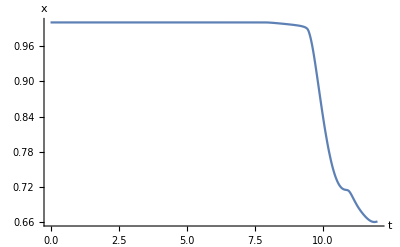
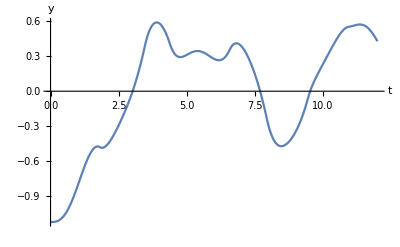
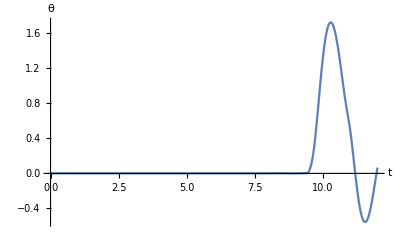

```mathematica
{Plot[{X1[t]}/.sol1,{t,0,T},AxesLabel->{"t","x"},PlotRange->All],
Plot[{X3[t]}/.sol1,{t,0,T},AxesLabel->{"t","y"},PlotRange->All],
Plot[{X5[t]}/.sol1,{t,0,T},AxesLabel->{"t","θ"},PlotRange->All]}
```

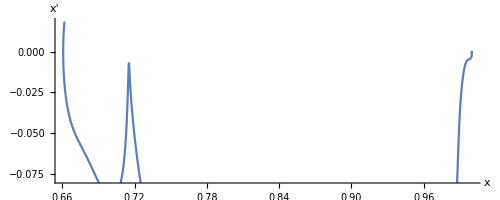
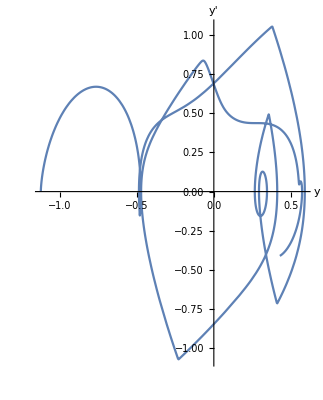
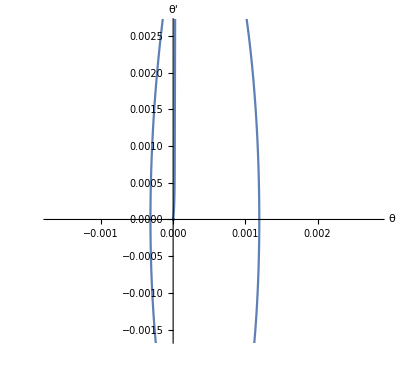

```mathematica
{ParametricPlot[{X1[t],X2[t]}/.sol1,{t,0,T},AxesLabel->{"x","x'"}],
ParametricPlot[{X3[t],X4[t]}/.sol1,{t,0,T},AxesLabel->{"y","y'"}],
ParametricPlot[{X5[t],X6[t]}/.sol1,{t,0,T},AxesLabel->{"θ","θ'"}]}
(*DrawAnimation*)
Animate[DrawSystem[Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[x, p],Subscript[y, p],θp,Subscript[w, p]][[1]]/.({(Subscript[x, p]->X1[t]/.sol1)[[1]],(Subscript[y, p]->X3[t]/.sol1)[[1]],(θp->X5[t]/.sol1)[[1]],Subscript[x, 1]->0,
Subscript[x, 2]->2 Subscript[w, p],Subscript[y, 1]->0,Subscript[y, 2]->0,EquibInputConditions}//Flatten)(*/.EquibInputConditions*)/.NumericParametersTest,{t,0,T}]
```

```mathematica
add both a driving force and damping
```

```mathematica
NumericTestParams
NumericParametersTest
EquibInputConditions
```

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→y_1[t]}

```mathematica
d
```

d

```mathematica
Ω=2; (* Hz *)
d=0.82 (*NonDim magnitude*)
EquibInputConditions={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0+d Sin[Ω t],Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]}
(SymetricEOMtoInvestigate=EOM/.greekTermsSymetricCase//.EquibInputConditions)/.dispNoTime//MatrixForm//TraditionalForm
```

0.82

{x_1[t]→0,y_1[t]→0.82 Sin[2 t],x_2[t]→2 w_p,y_2[t]→y_1[t]}

(x_p''
y_p''
θ_p'')==((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p) (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(0.82 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2)))+(sin(θ_p) h_p+cos(θ_p) w_p-x_p) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(0.82 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2)))-c_1 x_p'
-γ+(1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(0.82 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (0.82 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)+(1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(0.82 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2))) (0.82 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)-c_2 y_p'
-α (w_p (sin(θ_p) x_p+cos(θ_p) (0.82 sin(2 t)-y_p))+h_p (sin(θ_p) (0.82 sin(2 t)-y_p)-cos(θ_p) x_p)) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(0.82 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2)))-α (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(0.82 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (h_p (cos(θ_p) (2 w_p-x_p)+sin(θ_p) (0.82 sin(2 t)-y_p))+w_p (sin(θ_p) (2 w_p-x_p)+cos(θ_p) (y_p-0.82 sin(2 t))))-c_3 θ_p')

```mathematica
"Because of energy conservation one can clearly never get chaos from the motion of a single degree of freedom. We therefore add both a driving force and damping, in order to remove energy conservation"
```

```mathematica
EOMtoSolve=SymetricEOMtoInvestigate/.NumericTestParams/.NumericParametersTest/.NumericStructuralDamping;
numericEqs={X1'[t]==X2[t],
X2'[t]== (EOMtoSolve[[2,1]][[1]]),
X3'[t]==X4[t],
X4'[t]== (EOMtoSolve[[2,2]][[1]]),
X5'[t]==X6[t],
X6'[t]== (EOMtoSolve[[2,3]][[1]])}/.Subscript[x, p][t]->X1[t]/.Subscript[y, p][t]->X3[t]/.Subscript[θ, p][t]->X5[t]/.D[Subscript[x, p][t],t]->X2[t]/.D[Subscript[y, p][t],t]->X4[t]/.D[Subscript[θ, p][t],t]->X6[t];
NumericTestParams
NumericParametersTest
(*startValues={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==0.01,X5[0]==0,X6[0]==0.001}/.NumericTestParams/.NumericParametersTest*)
startValues={X1[0]==Subscript[w, p],X2[0]==0.00,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==0.0,X5[0]==0,X6[0]==0.00}/.NumericTestParams/.NumericParametersTest
T=12
sol1 = NDSolve[ {numericEqs, startValues}, {X1, X2,X3,X4,X5,X6}, {t, 0, T} ]
{ParametricPlot[{X1[t],X2[t]}/.sol1,{t,0,T},AxesLabel->{"x","x'"}],
ParametricPlot[{X3[t],X4[t]}/.sol1,{t,0,T},AxesLabel->{"y","y'"}],
ParametricPlot[{X5[t],X6[t]}/.sol1,{t,0,T},AxesLabel->{"θ","θ'"}]}
```

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{X1[0]==1,X2[0]==0.,X3[0]==-1.12453,X4[0]==0.,X5[0]==0,X6[0]==0.}

12

{{X1→InterpolatingFunction[{{0., 12.}}, <>],X2→InterpolatingFunction[{{0., 12.}}, <>],X3→InterpolatingFunction[{{0., 12.}}, <>],X4→InterpolatingFunction[{{0., 12.}}, <>],X5→InterpolatingFunction[{{0., 12.}}, <>],X6→InterpolatingFunction[{{0., 12.}}, <>]}}

{-Graphics-,-Graphics-,-Graphics-}